```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/FEinterpolants.nb"]
```

```mathematica
dir=NotebookDirectory[];
SetDirectory@dir;
```

## mtx

```mathematica
A11=Import["system/A11.rua"];
B1=Import["system/B1.rra"];
B2=Import["system/B2.rra"];
```

```mathematica
A=ArrayFlatten[{{A11,0},{0,A11}}];
B=ArrayFlatten[{{B1,B2}}];
```

```mathematica
MatrixPlot@A
```

```mathematica
MatrixPlot@B
```

```mathematica
𝒜=ArrayFlatten[{{A,Transpose@B},{B,0}}];
```

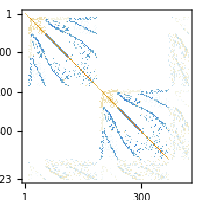

```mathematica
Show[MatrixPlot[𝒜],ImageSize->200]
```

```mathematica
b=Import["system/b.dat"][[1]];
```

```mathematica
Export["system/SPM.rua",𝒜]
```

## mtx prop

```mathematica
Det@A
```

```mathematica
Det@𝒜
```

```mathematica
MatrixPlot@B
```

```mathematica
MatrixRank@B
Length@NullSpace@B
```

```mathematica
NullSpace@Transpose@B
```

```mathematica
data=Eigenvalues@𝒜
```

```mathematica
Sort[Norm/@data];
```

```mathematica
spplot=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];

Show[spplot,Graphics@Circle[{0,0},1]]
```

## soln

```mathematica
z=Import["x.dat"][[1]];
```

```mathematica
z=LinearSolve[𝒜,b,Method->{
"Krylov",
Method->"BiCGSTAB",
"MaxIterations"->Automatic,
"StartingVector"->Table[0.,{Length@b}],
"Preconditioner"->None,
"Tolerance"->10^-10
}];
```

```mathematica
Norm[b-𝒜.z]
```

```mathematica
n=Length@A;
vel1=z[[;;n/2]];
vel2=z[[n/2+1;;n]];
velmag=Table[Norm[{vel1[[i]],vel2[[i]]}],{i,Length@vel1}];
pre=z[[n+1;;]];
```

```mathematica
𝒯=import["mesh.ntr"];
highlight[𝒯,{"nodesNumn","ribsNumn","trianglesNumn"}]
```

-Graphics-

```mathematica
numbOf𝓃@𝒯+numbOf𝓇@𝒯
```

185

```mathematica
pressureFE=ΔP0L;
velocityFE=ΔP1CR;
```

```mathematica
ph=𝒫[pre,pressureFE,𝒯];
(*pplot=plot𝒫ξ[ph,𝒯];*)
```

```mathematica
densityPlot𝒫ξ[ph,𝒯,{Min@pre,Max@pre},"DarkRainbow",True]
```

```mathematica
Show[Plot3D[Subscript[p, 0][x,y],{x,y}∈Ω,Mesh->None,PlotStyle->LightBlue],plot𝒫ξ[ph,𝒯],ImageSize->Medium]
```

```mathematica
computeErrorNorm[Subscript[p, 0],ph,𝒯]
```

```mathematica
v1h=𝒫[vel1,velocityFE,𝒯];
v2h=𝒫[vel2,velocityFE,𝒯];
velmagh=𝒫[velmag,velocityFE,𝒯];
```

```mathematica
Show[densityPlot𝒫ξ[velmagh,𝒯,{Min@velmag,Max@velmag},"DeepSeaColors",False],vectorPlot𝒫ξand𝒫η[v1h,v2h,𝒯]]
```

```mathematica
v1plot=plot𝒫ξ[v1h,𝒯];
v2plot=plot𝒫ξ[v2h,𝒯];
```

```mathematica
Show[Plot3D[u[x,y][[1]],{x,y}∈Ω,Mesh->None,PlotStyle->LightBlue],v1plot,ImageSize->Medium]
Show[Plot3D[u[x,y][[2]],{x,y}∈Ω,Mesh->None,PlotStyle->LightBlue],v2plot,ImageSize->Medium]
```